# Type II model

## Modelling the Hamiltonian in Eq. (11) in Chiral anomaly and longitudinal magnetotransport in type-II Weyl semimetals

```mathematica
x[k_]:=k[[1]]
y[k_]:=k[[2]]
z[k_]:=k[[3]]
```

```mathematica
HI[k_]:=((Cos[y[k]] + Cos[z[k]] - 2) m  + 2 t (Cos[x[k]] - Cos[k0])) PauliMatrix[1] - 2 t Sin[y[k]] PauliMatrix[2] - 2 t Sin[z[k]] PauliMatrix[3]
```

```mathematica
HII[k_]:=HI[k] + γ (Cos[x[k]] - Cos[k0]) PauliMatrix[0]
```

```mathematica
Plot3D[HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.005, k0->Pi/2}, {kx, -2, 2}, {ky, -2, 2}]
```

-Graphics3D-

```mathematica
HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.005, k0->Pi/2}
```

{{0,-0.01 Cos[kx]+0.15 (-1+Cos[ky])-(0.+0.01 ⅈ) Sin[ky]},{-0.01 Cos[kx]+0.15 (-1+Cos[ky])+(0.+0.01 ⅈ) Sin[ky],0}}

### Linearization

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, kz}]]
```

{1/2 (-2 γ Cos[k0]+2 γ Cos[kx]-√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[k0-kx]-16 m t Cos[kx]+4 t^2 Cos[2 kx]-8 t^2 Cos[k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[kx+kz]+2 m^2 Cos[ky+kz])),1/2 (-2 γ Cos[k0]+2 γ Cos[kx]+√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[k0-kx]-16 m t Cos[kx]+4 t^2 Cos[2 kx]-8 t^2 Cos[k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[kx+kz]+2 m^2 Cos[ky+kz]))}

```mathematica
eigvals/.{kx->kx+k0}
```

{1/2 (-2 γ Cos[k0]+2 γ Cos[k0+kx]-√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[kx]-16 m t Cos[k0+kx]+4 t^2 Cos[2 (k0+kx)]-8 t^2 Cos[2 k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[k0+kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[k0+kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[k0+kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[k0+kx+kz]+2 m^2 Cos[ky+kz])),1/2 (-2 γ Cos[k0]+2 γ Cos[k0+kx]+√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[kx]-16 m t Cos[k0+kx]+4 t^2 Cos[2 (k0+kx)]-8 t^2 Cos[2 k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[k0+kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[k0+kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[k0+kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[k0+kx+kz]+2 m^2 Cos[ky+kz]))}

```mathematica
FullSimplify[%]
```

{-γ Cos[k0]+γ Cos[k0+kx]-√(5 m^2+8 t^2+8 m t Cos[k0]+2 t^2 Cos[2 k0]-4 t^2 Cos[kx]-8 m t Cos[k0+kx]+2 t^2 Cos[2 (k0+kx)]-4 t^2 Cos[2 k0+kx]-2 m t Cos[k0-ky]+2 m t Cos[k0+kx-ky]-4 m^2 Cos[ky]+1/2 m^2 Cos[2 ky]-2 t^2 Cos[2 ky]-2 m t Cos[k0+ky]+2 m t Cos[k0+kx+ky]+2 m (2 t (-Cos[k0]+Cos[k0+kx])+m (-2+Cos[ky])) Cos[kz]+1/2 (m^2-4 t^2) Cos[2 kz]),-γ Cos[k0]+γ Cos[k0+kx]+√(5 m^2+8 t^2+8 m t Cos[k0]+2 t^2 Cos[2 k0]-4 t^2 Cos[kx]-8 m t Cos[k0+kx]+2 t^2 Cos[2 (k0+kx)]-4 t^2 Cos[2 k0+kx]-2 m t Cos[k0-ky]+2 m t Cos[k0+kx-ky]-4 m^2 Cos[ky]+1/2 m^2 Cos[2 ky]-2 t^2 Cos[2 ky]-2 m t Cos[k0+ky]+2 m t Cos[k0+kx+ky]+2 m (2 t (-Cos[k0]+Cos[k0+kx])+m (-2+Cos[ky])) Cos[kz]+1/2 (m^2-4 t^2) Cos[2 kz])}

```mathematica
Series[%30, {kx, 0, 1}, {ky, 0,1}, {kz, 0,1}]//Normal
```

%30

```mathematica
Cos[PlusMinus[k0]+kx]-Cos[k0]
```

-Cos[k0]+Cos[kx+±k0]

```mathematica
Series[%, {kx, 0,1}]//Normal
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
FullSimplify[%]
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
Refine[%, k0 ∈Reals]
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
TrigExpand[%]
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05}]
```

{1/2 (-0.3 Cos[k0]+0.3 Cos[kx]-√((0.195+0. ⅈ)-0.12 Cos[k0]+0.02 Cos[2 k0]-0.04 Cos[k0-kx]+0.12 Cos[kx]+0.02 Cos[2 kx]-0.04 Cos[k0+kx]+0.06 Cos[k0-ky]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]+0.06 Cos[k0+ky]-0.06 Cos[kx+ky])),1/2 (-0.3 Cos[k0]+0.3 Cos[kx]+√((0.195+0. ⅈ)-0.12 Cos[k0]+0.02 Cos[2 k0]-0.04 Cos[k0-kx]+0.12 Cos[kx]+0.02 Cos[2 kx]-0.04 Cos[k0+kx]+0.06 Cos[k0-ky]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]+0.06 Cos[k0+ky]-0.06 Cos[kx+ky]))}

```mathematica
tmp[k0_]:=eigvals/.k0->k0
```

```mathematica
Manipulate[
Plot3D[
Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05}]/.k0->x,
 {kx, -Pi, Pi}, {ky, -Pi, Pi}
],
{x, 0, Pi/2}
]
```

```mathematica
Eigenvalues[HII[{kx, 0, 0}]/.{ γ->0, m->0.15, t->-0.05}]/.k0->Pi/6
```

{-0.1 ((√3)/2-1. Cos[kx]),0.1 ((√3)/2-1. Cos[kx])}

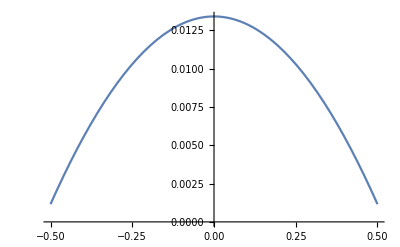

```mathematica
Plot[
-0.1((√3)/2-1.Cos[kx]),
 {kx, -0.5, 0.5}
]
```

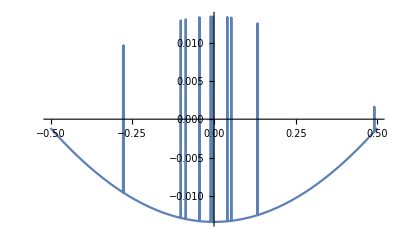

```mathematica
Plot[
(Last[Eigenvalues[HII[{kx, 0, 0}]/.{ γ->0, m->0.15, t->-0.05}]/.k0->Pi/6]),
 {kx, -0.5, 0.5}
]
```

```mathematica
Manipulate[
Plot[
Eigenvalues[HII[{kx, 0, 0}]/.{ γ->g, m->0.15, t->-0.05}]/.k0->x,
 {kx, -Pi, Pi},PlotRange->{-0.4, 0.2}
],
{x, 0, Pi/2},
{g, 0,0.15}
]
```

```mathematica
funcs[kx_, ky_, k0_]=Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.05}];
typeiiplots = Table[
Plot3D[
funcs[kx, ky, k0],
 {kx, -Pi*1.2, Pi*1.2}, {ky, -Pi, Pi},
PlotPoints->66,MaxRecursion->3,ImageSize->Medium, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]},
ViewPoint->{0,-4,0.5},Boxed->False
],
{k0,Subdivide[Pi/2, 2]}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[
funcs[kx, ky, 0],
 {kx, -Pi*1.2, Pi*1.2}, {ky, -Pi, Pi},
PlotPoints->66,MaxRecursion->3,ImageSize->Medium, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]},
ViewPoint->{0,-4,0.5},Boxed->False
]
```

-Graphics3D-

```mathematica
MapIndexed[Export[
FileNameJoin[{NotebookDirectory[],ToString[First[#2]]<>".png"}]
, #1, ImageResolution->300]&, typeiiplots]
```

{/home/thorvald/Documents/NTNU/10semester/mathematica/1.png,/home/thorvald/Documents/NTNU/10semester/mathematica/2.png,/home/thorvald/Documents/NTNU/10semester/mathematica/3.png}

```mathematica
FileNameJoin[{NotebookDirectory[],"MyPackages"}]
```

/home/thorvald/Documents/NTNU/10semester/mathematica/MyPackages

```mathematica
funcs[kx, ky, k0]
```

{-√(0.0225-0.03 Cos[k0]+0.01 Cos[k0]^2+0.03 Cos[kx]-0.02 Cos[k0] Cos[kx]+0.01 Cos[kx]^2-0.045 Cos[ky]+0.03 Cos[k0] Cos[ky]-0.03 Cos[kx] Cos[ky]+0.0225 Cos[ky]^2+0.01 Sin[ky]^2),√(0.0225-0.03 Cos[k0]+0.01 Cos[k0]^2+0.03 Cos[kx]-0.02 Cos[k0] Cos[kx]+0.01 Cos[kx]^2-0.045 Cos[ky]+0.03 Cos[k0] Cos[ky]-0.03 Cos[kx] Cos[ky]+0.0225 Cos[ky]^2+0.01 Sin[ky]^2)}

```mathematica
Plot3D[
Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05, k0->Pi/2 /3}],
 {kx, -Pi, Pi}, {ky, -Pi, Pi}
]
```

-Graphics3D-

```mathematica
Export["./a.png",%45,"PNG"]
```

./a.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["./a.png"]]]
```

```mathematica
Plot3D[
funcs[kx, ky, 1],
{kx, -Pi, Pi}, {ky, -Pi, Pi}
]
```

-Graphics3D-

```mathematica
Show[%89,Axes->False]
```

Show::gtype: Out is not a type of graphics.

Show[%89,Axes→False]

```mathematica
Show[%118,Boxed->False]
```

Show::gtype: Out is not a type of graphics.

Show[%118,Boxed→False]

```mathematica
ref/Method
```

ref/Method

```mathematica
Plot3D[funcs[kx,ky,1],{kx,-π,π},{ky,-π,π},Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

### Plotting realistic briouille zone

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05, k0->Pi/2}]
```

{1/2 (0.3 Cos[kx]-√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky])),1/2 (0.3 Cos[kx]+√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky]))}

```mathematica
Plot3D[eigvals, {kx, -Pi, Pi}, {ky, -Pi, Pi}, ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[eigvals,{kx,-π,π},{ky,-π,π},PlotPoints->66,MaxRecursion->3,ImageSize->Large, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]}, Lighting->"ThreePoint"]
```

-Graphics3D-

```mathematica
Show[%23,ViewPoint->Front]
```

-Graphics-

```mathematica
Plot3D[eigvals,{kx,-π,π},{ky,-π,π},Filling->Bottom,PlotPoints->66,MaxRecursion->3,ImageSize->Large]
```

-Graphics3D-

### Ridgeline plot one dim

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.{ m->0.15, t->-0.05, k0->Pi/2}]
```

{1/2 (2 γ Cos[kx]-√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky])),1/2 (2 γ Cos[kx]+√((0.175+0. ⅈ)+0.12 Cos[kx]+0.02 Cos[2 kx]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]-0.06 Cos[kx+ky]))}

```mathematica
Table[
{kx, γ},
{γ, {0, 0.1, 0.15}},
{kx, -1, 1, 0.1}
]
```

{{{-1.,0},{-0.9,0},{-0.8,0},{-0.7,0},{-0.6,0},{-0.5,0},{-0.4,0},{-0.3,0},{-0.2,0},{-0.1,0},{0.,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0}},{{-1.,0.1},{-0.9,0.1},{-0.8,0.1},{-0.7,0.1},{-0.6,0.1},{-0.5,0.1},{-0.4,0.1},{-0.3,0.1},{-0.2,0.1},{-0.1,0.1},{0.,0.1},{0.1,0.1},{0.2,0.1},{0.3,0.1},{0.4,0.1},{0.5,0.1},{0.6,0.1},{0.7,0.1},{0.8,0.1},{0.9,0.1},{1.,0.1}},{{-1.,0.15},{-0.9,0.15},{-0.8,0.15},{-0.7,0.15},{-0.6,0.15},{-0.5,0.15},{-0.4,0.15},{-0.3,0.15},{-0.2,0.15},{-0.1,0.15},{0.,0.15},{0.1,0.15},{0.2,0.15},{0.3,0.15},{0.4,0.15},{0.5,0.15},{0.6,0.15},{0.7,0.15},{0.8,0.15},{0.9,0.15},{1.,0.15}}}

```mathematica
ListLinePlot3D[
{Table[
First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
],
Table[
Last[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
},
Filling->Axis
]
```

-Graphics3D-

```mathematica
bottom=ListLinePlot3D[
Table[
First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
,
Filling->Bottom
]
top=ListLinePlot3D[
Table[
Last[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
,
Filling->Top,
FillingStyle->{Opacity[0.1]}
]
Show[top,bottom, PlotRange->{-0.2, 0.2}, BoxRatios->{1, 2, 0.3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Show[%143,ViewPoint->{0,∞,0}]
```

Show::gtype: Out is not a type of graphics.

Show[%143,ViewPoint→{0,∞,0}]

```mathematica
r som bor sammen med noen som er smittet og trenger daglig testing for å slippe karantene kan få utdelt 5 test
```

5 å bor daglig er få for kan karantene med noen og r sammen slippe smittet som^2 test testing trenger utdelt

```mathematica
Export["/home/thorvald/Documents/NTNU/10semester/notes/figures/typeIIridgeline.png",%143,"PNG"]
```

/home/thorvald/Documents/NTNU/10semester/notes/figures/typeIIridgeline.png

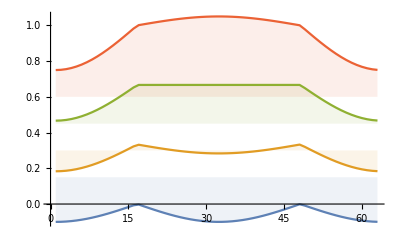

```mathematica
ListLinePlot[
Table[
γ /0.15+First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
,
Filling->Table[n->n*0.15, {n, 4}],
FillingStyle->{Opacity[0.1]}
]
```

```mathematica
Table[n->n, {n, Subdivide[0.15, 3]}]
```

{0.→0.,0.05→0.05,0.1→0.1,0.15→0.15}

```mathematica
Table[n->n/0.15, {n, Subdivide[0.15, 3]}]
```

{0.→0.,0.05→0.333333,0.1→0.666667,0.15→1.}